### Test BR_aa=1

```mathematica
Quit[]
```

```mathematica
data=Import["~/Software/acropolis/tst.dat"];
data[[1]]
```

{1000.,9.999999999999999988×10^-15,0.,0.752507899999957264,0.0000183792399999989577,0.,7.75538032999956623×10^-6,0.06185800999999648,8.10474899999979646×10^-15,4.08745259999976775×10^-10,0.,0.,0.752573399999957204,0.0000179224799999989787,0.,7.83537462999956215×10^-6,0.0618417999999964843,2.6269949999998786×10^-14,4.37593159999975133×10^-10,0.,0.,0.752442499999957271,0.0000188398199999989295,0.,7.68602713999957009×10^-6,0.0618741799999964828,1.26003800000016864×10^-15,3.82641399999978251×10^-10,0.}

```mathematica
ToLinearScale[list_]:={10^list[[1]],10^list[[2]]}
```

```mathematica
dataDoverHmean=Table[{Log10[data[[i,1]]],Log10[data[[i,2]]],Log10[data[[i,5]]/data[[i,4]]]},{i,1,Length[data]}];
dataHe3overDmean=Table[{Log10[data[[i,1]]],Log10[data[[i,2]]],Log10[data[[i,7]]/data[[i,5]]]},{i,1,Length[data]}];
dataDoverHhigh=Table[{Log10[data[[i,1]]],Log10[data[[i,2]]],Log10[data[[i,14]]/data[[i,13]]]},{i,1,Length[data]}];
dataHe3overDhigh=Table[{Log10[data[[i,1]]],Log10[data[[i,2]]],Log10[data[[i,16]]/data[[i,14]]]},{i,1,Length[data]}];dataDoverHlow=Table[{Log10[data[[i,1]]],Log10[data[[i,2]]],Log10[data[[i,23]]/data[[i,22]]]},{i,1,Length[data]}];
dataHe3overDlow=Table[{Log10[data[[i,1]]],Log10[data[[i,2]]],Log10[data[[i,25]]/data[[i,23]]]},{i,1,Length[data]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

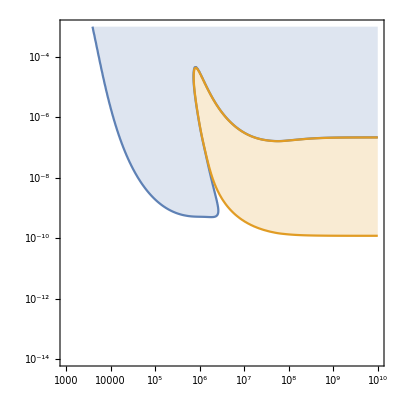

```mathematica
DoverHobs=2.547*10^-5;
DoverHerr=0.035*10^-5;
ListContourPlot[dataDoverHhigh,Contours->{Log10[DoverHobs+2*DoverHerr]},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
ListContourPlot[dataDoverHlow,Contours->{Log10[DoverHobs-2*DoverHerr]},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt1=ListLogLogPlot[{%,%%%%},Joined->True,Filling->Top,PlotRange->{{10^3,10^10},{10^-14,10^-3}},Frame->True,AspectRatio->1,LabelStyle->Larger]
```

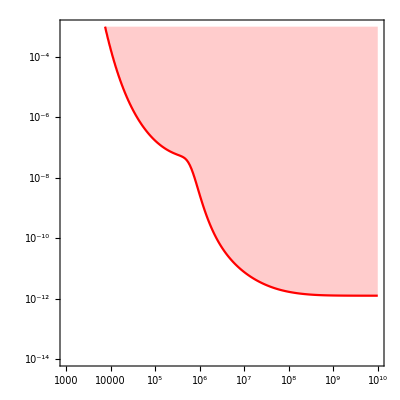

```mathematica
He3overDobs=0.83;
He3overDerr=0.15;
ListContourPlot[dataHe3overDhigh,Contours->{Log10[He3overDobs+2*He3overDerr]},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt2=ListLogLogPlot[{%},Joined->True,Filling->Top,PlotRange->{{10^3,10^10},{10^-14,10^-3}},Frame->True,AspectRatio->1,LabelStyle->Larger,PlotStyle->Red]
```

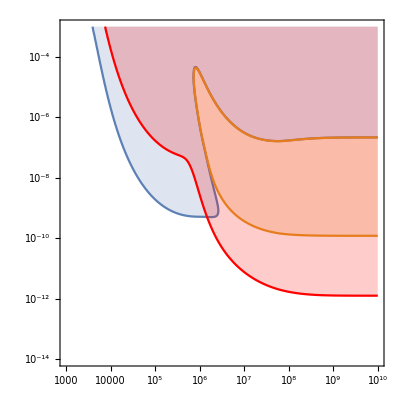

```mathematica
Show[plt1,plt2]
```

### Test BR_ee=1

```mathematica
Quit[]
```

```mathematica
data=Import["~/Software/acropolis/tst_ee.dat"];
data[[1]]
```

{1.,9.999999999999999988×10^-15,0.,0.752507900000000007,0.0000183792400000000013,0.,7.75538032999999991×10^-6,0.061858009999999998,8.10474899999999999×10^-15,4.08745259999999988×10^-10,0.,0.,0.752573399999999948,0.0000179224799999999985,0.,7.83537463000000091×10^-6,0.0618418000000000023,2.62699500000000008×10^-14,4.3759316×10^-10,0.,0.,0.752442500000000014,0.0000188398200000000002,0.,7.68602714000000038×10^-6,0.0618741800000000009,1.26003800000000002×10^-15,3.82641400000000016×10^-10,0.}

```mathematica
ToLinearScale[list_]:={10^list[[1]],10^list[[2]]}
```

```mathematica
dataDoverHmean=Table[{Log10[data[[i,1]]],Log10[data[[i,2]]],Log10[data[[i,5]]/data[[i,4]]]},{i,1,Length[data]}];
dataHe3overDmean=Table[{Log10[data[[i,1]]],Log10[data[[i,2]]],Log10[data[[i,7]]/data[[i,5]]]},{i,1,Length[data]}];
dataDoverHhigh=Table[{Log10[data[[i,1]]],Log10[data[[i,2]]],Log10[data[[i,14]]/data[[i,13]]]},{i,1,Length[data]}];
dataHe3overDhigh=Table[{Log10[data[[i,1]]],Log10[data[[i,2]]],Log10[data[[i,16]]/data[[i,14]]]},{i,1,Length[data]}];dataDoverHlow=Table[{Log10[data[[i,1]]],Log10[data[[i,2]]],Log10[data[[i,23]]/data[[i,22]]]},{i,1,Length[data]}];
dataHe3overDlow=Table[{Log10[data[[i,1]]],Log10[data[[i,2]]],Log10[data[[i,25]]/data[[i,23]]]},{i,1,Length[data]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
dataDoverHhigh
```

{{0.,-14.000000000000000001,-4.623150759525719717},{0.,-13.94472361809045145,-4.623150759525719717},39996,{3.,-3.055276381909546765,Indeterminate},{3.,-2.99999999999999999,Indeterminate}}
 |  |  |  |

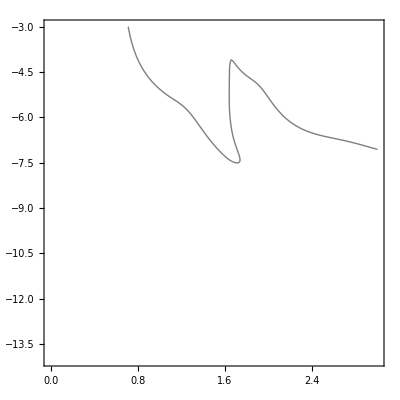

```mathematica
ListContourPlot[dataDoverHhigh,Contours->{-5},ContourShading->Log10[DoverHobs+2*DoverHerr]]
```

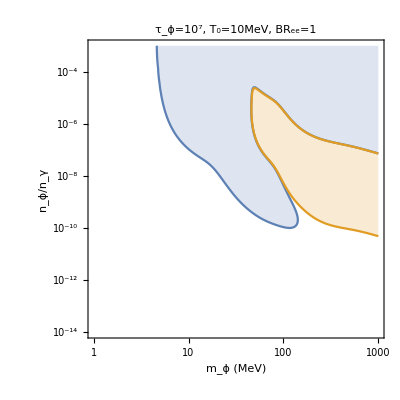

```mathematica
DoverHobs=2.547*10^-5;
DoverHerr=0.035*10^-5;
ListContourPlot[dataDoverHhigh,Contours->{Log10[DoverHobs+2*DoverHerr]},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
ListContourPlot[dataDoverHlow,Contours->{Log10[DoverHobs-2*DoverHerr]},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt1=ListLogLogPlot[{%,%%%%},Joined->True,Filling->Top,PlotRange->{{10^0,10^3},{10^-14,10^-3}},Frame->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"m_ϕ (MeV)","n_ϕ/n_γ"},PlotLabel->"τ_ϕ=10^7, T_0=10MeV, BR_ee=1"]
```

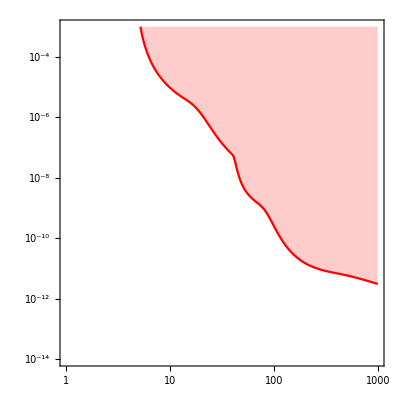

```mathematica
He3overDobs=0.83;
He3overDerr=0.15;
ListContourPlot[dataHe3overDhigh,Contours->{Log10[He3overDobs+2*He3overDerr]},ContourShading->None];
Cases[Normal@%,Line[pts_,___]:>pts,Infinity][[1]];
Map[ToLinearScale,%];
plt2=ListLogLogPlot[{%},Joined->True,Filling->Top,PlotRange->{{10^0,10^3},{10^-14,10^-3}},Frame->True,AspectRatio->1,LabelStyle->Larger,PlotStyle->Red]
```

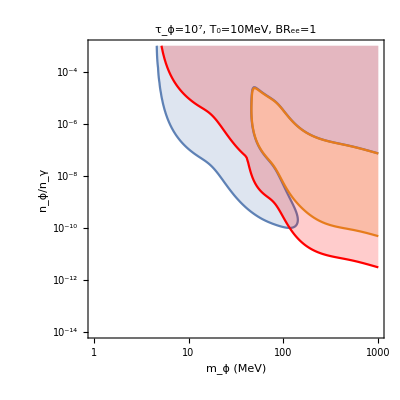

```mathematica
Show[plt1,plt2]
```